```mathematica
GaussianRandomMatrix[n_]:=Table[RandomVariate[NormalDistribution[]],n,n];
```

```mathematica
RealWignerMatrix[n_]:=Block[{rm,m1,m2},
rm = GaussianRandomMatrix[n];
m1  =UpperTriangularize[rm];
m2 = UpperTriangularize[rm,1];

m1+Transpose[m2]
];
GaussianOrthogonalEnsemble[n_]:=Block[{wm,goeScaling},
wm = RealWignerMatrix[n];
goeScaling = Table[If[i==j,√2,1],{i,1,n},{j,1,n}];

wm*goeScaling
];
```

```mathematica
MatrixForm[RealWignerMatrix[5]]
```

(-0.208524 | 0.960862 | -0.175705 | -0.978757 | -0.307465
0.960862 | -2.06367 | -0.112531 | -0.392601 | 0.461695
-0.175705 | -0.112531 | 0.939194 | 2.40116 | -0.439898
-0.978757 | -0.392601 | 2.40116 | 0.415876 | 0.229698
-0.307465 | 0.461695 | -0.439898 | 0.229698 | -2.352)

```mathematica
eigenValues = Flatten[Table[Eigenvalues[RealWignerMatrix[200]],1000]];
```

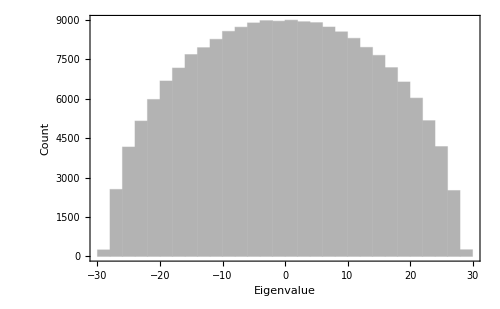

```mathematica
Histogram[eigenValues,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
ImageSize->500,
PlotRange->All,
FrameLabel->{Style["Eigenvalue",15], Style["Count",15]}
]
```

```mathematica
eigenValues = Flatten[Table[Eigenvalues[GaussianOrthogonalEnsemble[200]],1000]];
```

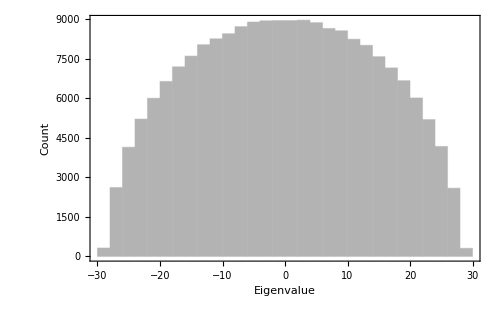

```mathematica
Histogram[eigenValues,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
ImageSize->500,
PlotRange->All,
FrameLabel->{Style["Eigenvalue",15], Style["Count",15]}
]
```

```mathematica
WhiteNoise[n_]:=RandomVariate[NormalDistribution[],n];
WishartOrthogonalEnsemble[n_,t_]:=Correlation[Transpose[Table[WhiteNoise[t],n]]];
```

```mathematica
randomTimeSeries = Table[WhiteNoise[200],50];
```

```mathematica
eigenWishart = Flatten[Table[Eigenvalues[WishartOrthogonalEnsemble[50,200]],1000]];
```

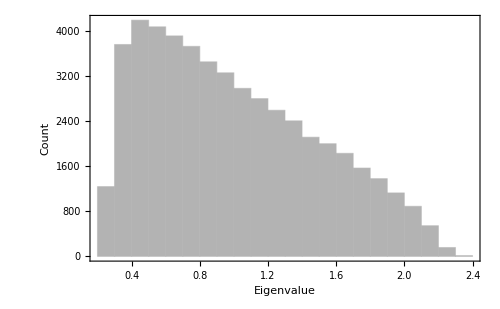

```mathematica
Histogram[eigenWishart,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
ImageSize->500,
PlotRange->All,
FrameLabel->{Style["Eigenvalue",15], Style["Count",15]}
]
```

```mathematica
MarchenkoPasturHighestEigenval[n_,t_,σ_]:=Block[{k=t/n},σ^2(k^(-1/2)+1)^2];
MarchenkoPasturLowestEigenval[n_,t_,σ_]:=Block[{k=t/n},σ^2(k^(-1/2)-1)^2];
MarchenkoPasturPDF[n_,t_,σ_,λ_]:=Block[{k,λPlus,λMinus},
k=t/n;
λPlus = MarchenkoPasturHighestEigenval[n,t,σ];
λMinus = MarchenkoPasturLowestEigenval[n,t,σ];

k/(2 π σ^2) (√((λPlus-λ)(λ-λMinus)))/λ
];
```

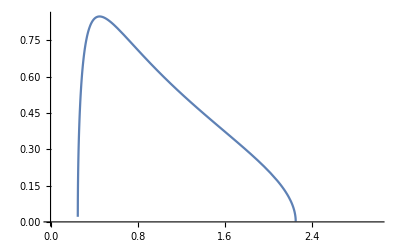

```mathematica
Plot[MarchenkoPasturPDF[50,200,1,λ],{λ,0,3}]
```